```mathematica
Get[StringJoin[NotebookDirectory[] , "article/nprimes.mx"]]
```

```mathematica
Max@nprimes
```

5000000

```mathematica
allPrimes=allPrimes[[2;;]];
```

```mathematica
allPrimes=allPrimes[[All,;;10000]];
```

```mathematica
fracs=Table[x/nprimes[k][[x]],{k,2,16},{x,10000}];
```

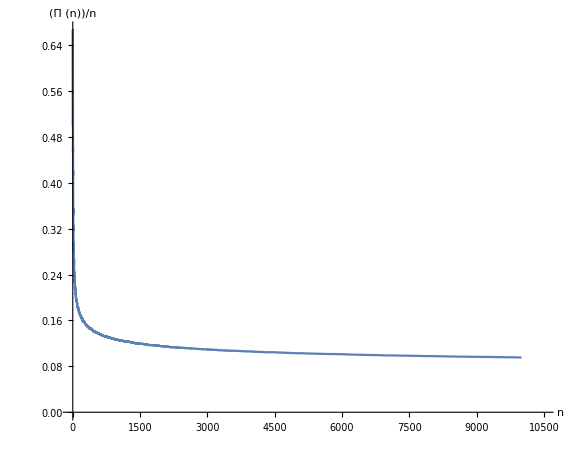
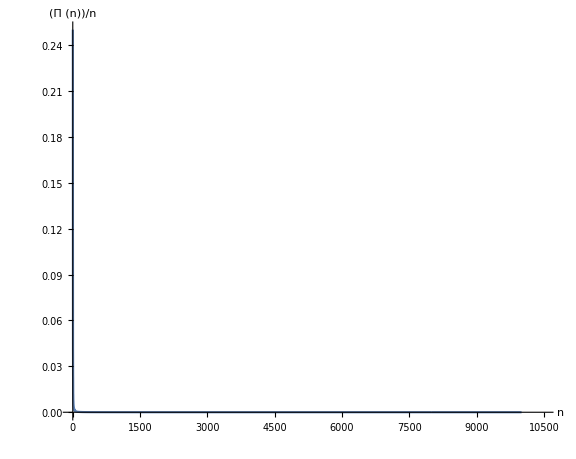
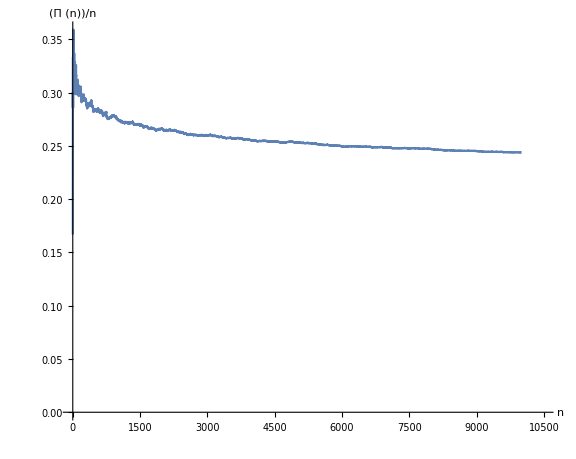
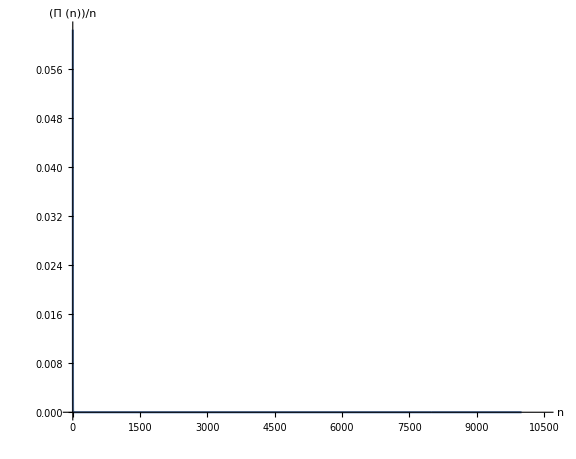
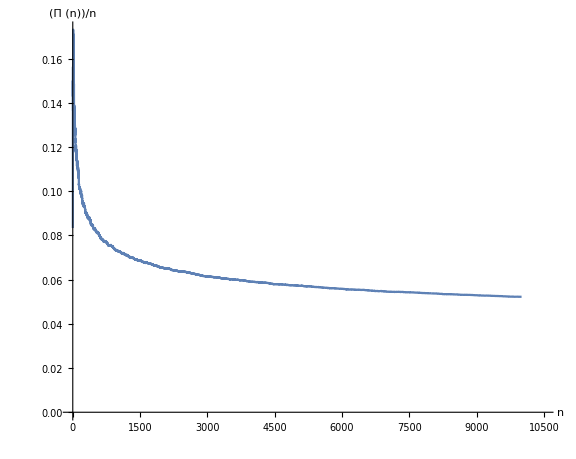
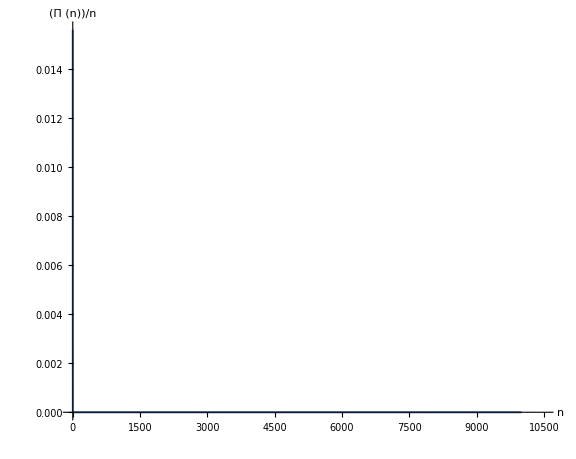
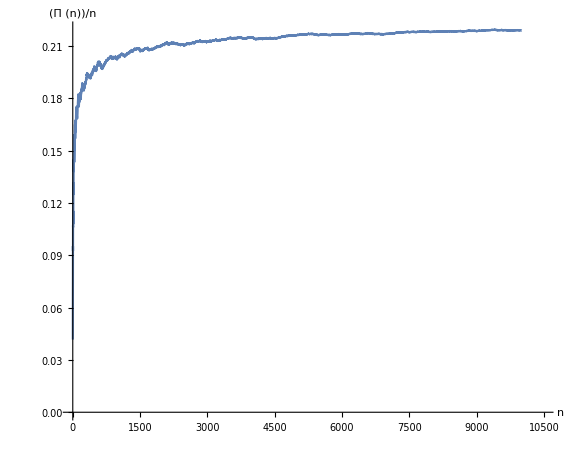
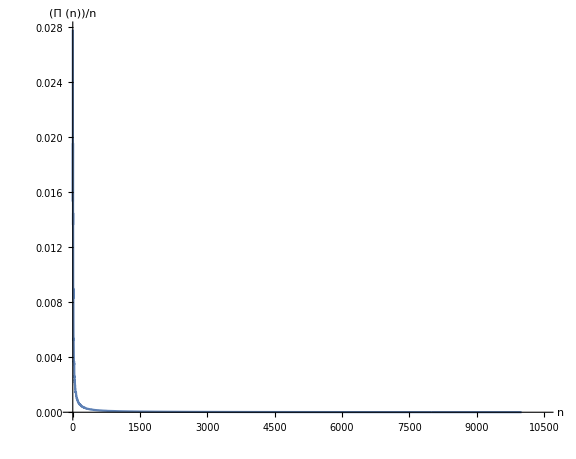
{-Graphics-d=2,-Graphics-d=3,-Graphics-d=4,-Graphics-d=5,-Graphics-d=6,-Graphics-d=7,-Graphics-d=8,-Graphics-d=9,-Graphics-d=10,-Graphics-d=11,-Graphics-d=12,-Graphics-d=13,-Graphics-d=14,-Graphics-d=15,-Graphics-d=16}

```mathematica
graphs=Table[Labeled[ListLinePlot[fracs[[x]],PlotRange->{{0,10490},All},AxesLabel->{Style["n",38, Italic],Style["(Π (n))/n", 38,Italic]},LabelStyle->Directive[18],ImageSize->Large,AspectRatio->0.8],Style["d="<>ToString[x+1],38],Top],{x,15}]
```

```mathematica
fig=Grid[Partition[graphs,3],Spacings->{Automatic, 4}]
```

-Graphics-d=2 | -Graphics-d=3 | -Graphics-d=4
-Graphics-d=5 | -Graphics-d=6 | -Graphics-d=7
-Graphics-d=8 | -Graphics-d=9 | -Graphics-d=10
-Graphics-d=11 | -Graphics-d=12 | -Graphics-d=13
-Graphics-d=14 | -Graphics-d=15 | -Graphics-d=16

```mathematica
Export[NotebookDirectory[]<>"counts.pdf",fig]
```

/home/blmayer/repos/thesis/counts.pdf

```mathematica
dens=Table[x/allPrimes[[k,x]],{k,10},{x,10000}];
```

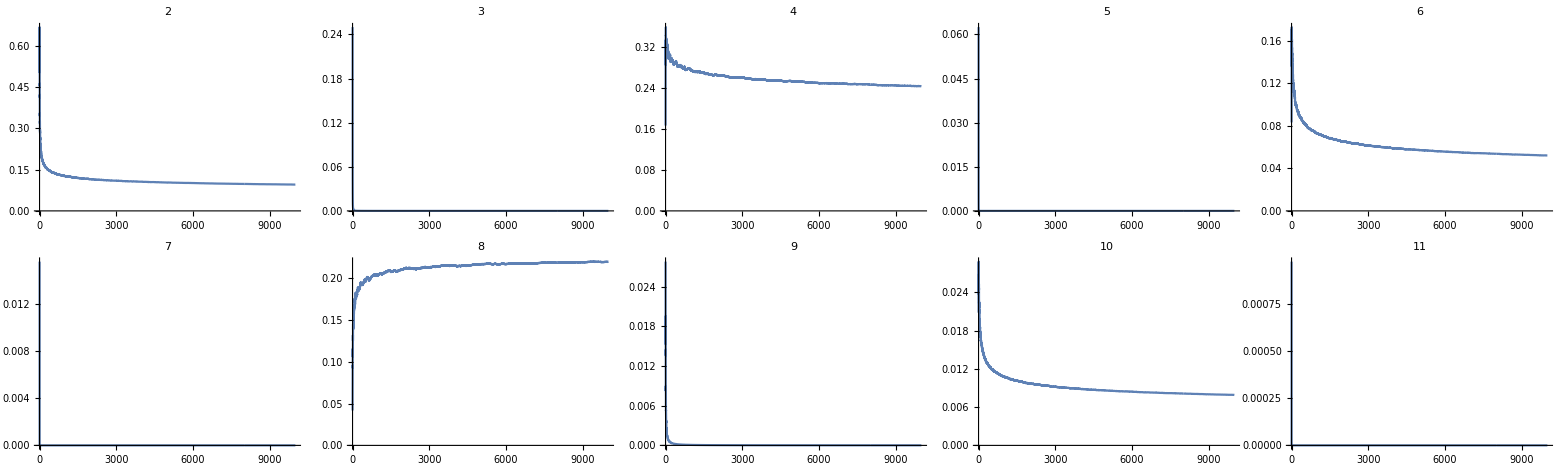
-Graphics-Prime density π(x)/x

```mathematica
Labeled[Grid[Partition[Table[ListLinePlot[dens[[x]],PlotRange->Full,PlotLabel->x+1],{x,10}],5]],"Prime density π(x)/x"]
```

```mathematica
Export["counts.pdf", %5]
```

densities.pdf

### Asymptotic properties

#### Case d = 2

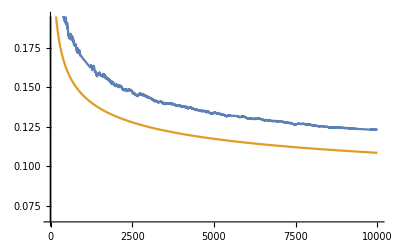

```mathematica
Plot[{PrimePi[x]/x,1/Log[x]},{x,1,10000}]
```

```mathematica
Asymptotic[PrimePi[x]/x,x->∞]
```

1/Log[x]

#### Case d is prime

```mathematica
allPrimes=Prepend[allPrimes,{1}];
```

```mathematica
primePiD[x_,d_]:=Select[Table[Prime[n]^(d-1),{n,x^(1/(d-1))}],#≤x&]//Length;
```

```mathematica
ClearAll[primePiD]
```

```mathematica
primePiD=.
```

```mathematica
d=3;x=100;Table[Prime[n]^(d-1),{n, x^(1/(d-1))}]
```

{4,9,25,49,121,169,289,361,529,841}

```mathematica
Prime[10]
```

29

```mathematica
primePiD[100,2]
```

25

```mathematica
PrimePi[100]
```

25

```mathematica
x^(1/3)//N
```

4.64159

```mathematica
x
```

100

```mathematica
d
```

3

```mathematica
Select[allPrimes[[3]],#<50&]
```

{4,9,25,49}

```mathematica
primePiD[1000,2]
```

168

```mathematica
Asymptotic[PrimePi[x],x->∞]
```

x/Log[x]

```mathematica
Table[DiscreteAsymptotic[primePiD[x,d]/x,x->∞],{d,{3,5,7,11}}]
```

Table::iterb: Iterator {n,√x} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {n,x^(1/4)} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Table::argm will be suppressed during this calculation.

{0,0,0,0}

```mathematica
DiscreteAsymptotic[primePiD[x,3]/x,x->∞]
```

Table::iterb: Iterator {n,√x} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

0

Power::infy: Infinite expression 1/0 encountered.

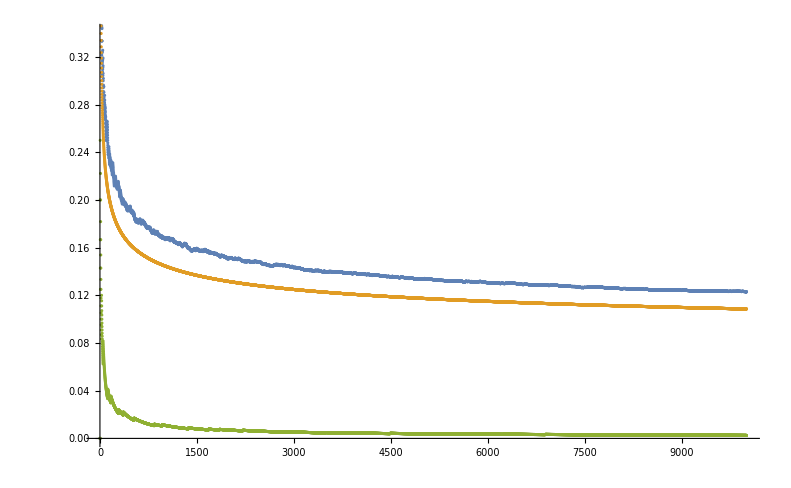

```mathematica
ListPlot[{Table[PrimePi[x]/x,{x,10000}],Table[1/Log[x],{x,10000}],Table[primePiD[x,3]/x,{x,10000}]}]
```

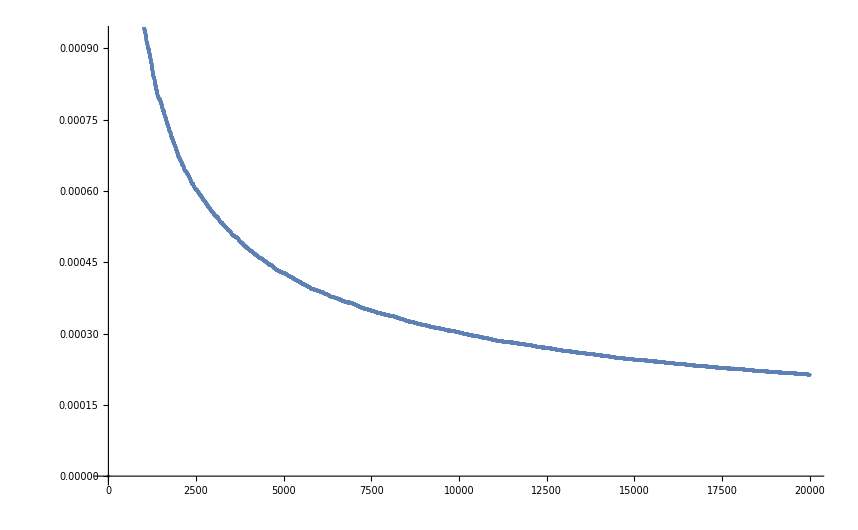

```mathematica
ListPlot[Table[ primePiD[x,3]/PrimePi[x],{x,2,100000000,5000}]]
```